Visualizing a small-world Allais gamble:

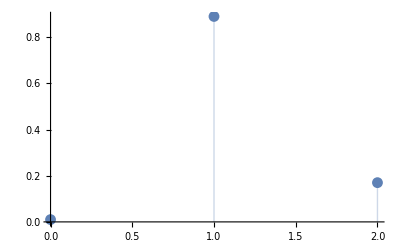

```mathematica
ListPlot[
Insert[Insert[Insert[{},{0,.01},1], {1,.89},2],{2,.17},3],
Filling->Axis
]
```

Visualizing the grand-world version that gamble:

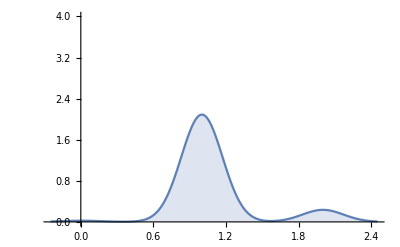

```mathematica
Plot[
.01*PDF[SkewNormalDistribution[0,.17,0],x]+.89*PDF[SkewNormalDistribution[1,.17,0],x]+
.1*PDF[SkewNormalDistribution[2,.17,0],x],
{x,-.25,2.45},
PlotRange->{0,4},Filling->Axis
]
```

The chance on this model that you’ll lead a life of at best zero utility despite winning $1M, given σ=.1:

```mathematica
CDF[NormalDistribution[1,.1],0]
```

7.61985×10^-24

Visualizing the same Allais gamble in the grand-world setting with Buchakian skew:

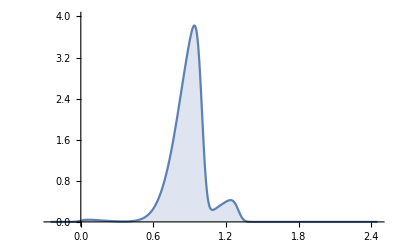

```mathematica
Plot[
.01*PDF[SkewNormalDistribution[0,.17,5],x]+.89*PDF[SkewNormalDistribution[1,.17,-5],x]+
.1*PDF[SkewNormalDistribution[1.3,.17,-5],x],
{x,-.25,2.45},
PlotRange->{0,4},Filling->Axis
]
```

The true standard deviation on the skewed model:

```mathematica
StandardDeviation[SkewNormalDistribution[1,.17,-5]]
```

0.105874

Skewing a normal distribution shrinks the standard deviation:

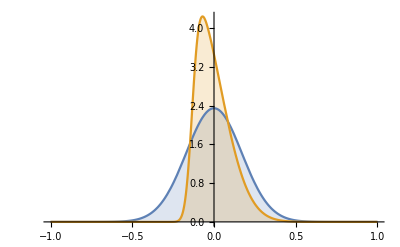

```mathematica
Plot[
{PDF[SkewNormalDistribution[0,.17,0],x],PDF[SkewNormalDistribution[-.133,.17,5],x]},
{x,-1,1},
Filling->Axis
]
```

The chance on Buchak’s skewed model that you’ll lead a life of at most utility zero, despite winning $1M:

```mathematica
CDF[SkewNormalDistribution[1,.17,-5],0]
```

4.04475×10^-9

The chance you’ll lead a life of at least utility 1.3, despite winning only $1M:

```mathematica
1-CDF[SkewNormalDistribution[1,.17,-5],1.3]
```

0.

The chance you’ll lead a life of at least utility 1.25, despite winning only $1M:

```mathematica
1-CDF[SkewNormalDistribution[1,.17,-5],1.25]
```

6.66134×10^-16

The chance on the unskewed model that you’ll lead a life of at least utility 1.3, despite winning only $1M:

```mathematica
1-CDF[NormalDistribution[1,.1],1.3]
```

0.0013499